### Rachel Krueger Che 164 Final Project Appendix

```mathematica
Part 1
```

```mathematica
(*Produces just an array with either probability (flag=0) or helmholtz free energy (flag=1)*)

getDist[J_,epsilon_,flag_]:=(counter=0;
(*J=0.4;
epsilon=0.2;*)
Ns=ConstantArray[0,{32}];
energies=ConstantArray[0,{32}];
spins={0,0,0,0,0};
numerators={0,0,0,0,0,0};
PofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
FofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
Q=0;
For[i=-1,i≤1,i+=2,
	For[j=-1,j≤1,j+=2,
		For[k=-1,k≤1,k+=2,
			For[l=-1,l≤1,l+=2,
				For[m=-1,m≤1,m+=2,
				(*Print[i ,j, k, l, m];*)
					spins[[1]]=i;
					spins[[2]]=j; 
					spins[[3]]=k;
					spins[[4]]=l;
					spins[[5]]=m;
					ends = -J*spins[[1]]-J*spins[[5]];
					nnTerms=0;
					counter++;
					For[x=1,x≤4,x++,
						nnTerms += -J*spins[[x]]*spins[[x+1]];
					];
					tubeTerms=0;
					For[y=1,y≤5,y++,
						tubeTerms += (N[4*epsilon*spins[[y]]]-0);(*this was the problematic line*)
						Ns[[counter]]+=(spins[[y]]+1)/2;
	
					];
					(*Print[N[tubeTerms]];*)
					etot=nnTerms+ends+tubeTerms;
					energies[[counter]]=etot
					(*Print[nnTerms,"   ",  tubeTerms ,"   ",  ends];*)
				];
		];
	];
];
];
For[z=1,z≤32,z++,
(*Print[z,"      ",       energies[[z]],"    ",Exp[-1*energies[[z]]],"   ",Q];*)
Q+=Exp[-1*energies[[z]]];
numerators[[Ns[[z]]+1]]+=Exp[-1*energies[[z]]];
(*Print[energies[[z]]];*)
];
For[q=1,q≤6,q++,
PofN[[q]][[2]]=numerators[[q]]/Q;
FofN[[q]][[2]]=-Log[PofN[[q]][[2]]];
];
p=0;
If[flag==1,Return[PofN]];
If[flag==0, Return[FofN]];
)
```

```mathematica
(*degenerate cases*)
```

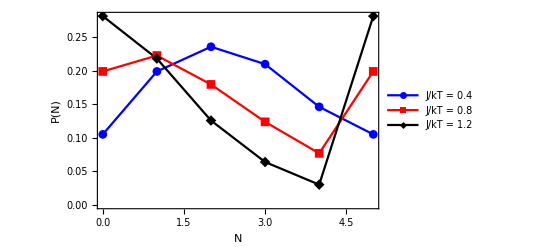

```mathematica
p1Probs=ListLinePlot[{getDist[0.4,0.04,1],getDist[0.8,0.08,1],getDist[1.2,0.12,1]},PlotMarkers->Automatic,FrameLabel->{"N","P(N)"},BaseStyle->{FontSize->14},PlotLegends->{"J/kT = 0.4","J/kT = 0.8","J/kT = 1.2"},PlotStyle->{{Blue},Red,Black},Frame->True]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig1.eps",p1Probs]
```

/Users/rachelkrueger/Documents/StatMech/fig1.eps

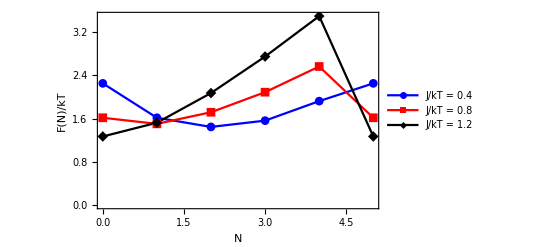

```mathematica
p1Fs=ListLinePlot[{getDist[0.4,0.04,0],getDist[0.8,0.08,0],getDist[1.2,0.12,0]},PlotMarkers->Automatic,FrameLabel->{"N","F(N)/kT"},PlotLegends->{"J/kT = 0.4","J/kT = 0.8","J/kT = 1.2"},BaseStyle->{FontSize->14},PlotStyle->{Blue,Red,Black},Frame->True]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig2.eps",p1Fs]
```

/Users/rachelkrueger/Documents/StatMech/fig2.eps

Part 2

```mathematica
(*J/kt = 1.2 corresponds to room-temperature water*)
```

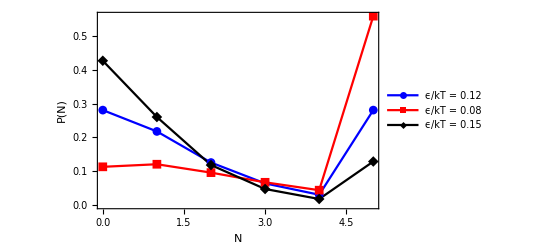

```mathematica
p2Ps=p1Probs=ListLinePlot[{getDist[1.2,0.12,1],getDist[1.2,0.08,1],getDist[1.2,0.15,1]},PlotMarkers->Automatic,FrameLabel->{"N","P(N)"},PlotLegends->{"ϵ/kT = 0.12","ϵ/kT = 0.08","ϵ/kT = 0.15"},BaseStyle->{FontSize->14},PlotStyle->{Blue,Red,Black},Frame->True]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig3.eps",p2Ps]
```

/Users/rachelkrueger/Documents/StatMech/fig3.eps